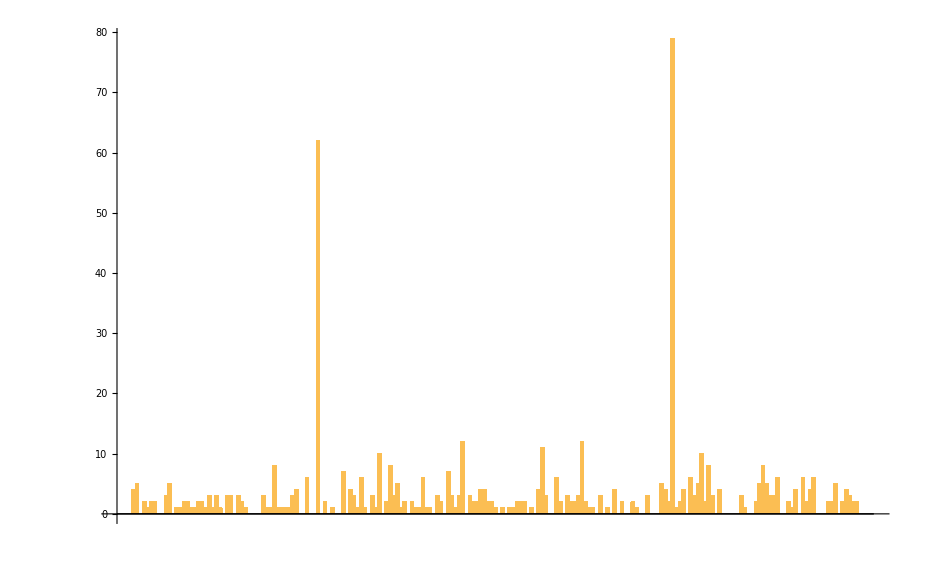

```mathematica
visit[n_]:= FromDigits @@ ToExpression[StringCases[
      StringCases[Import[StringJoin["https://www.netpad.net.cn/resource/works/", 
         ToString[n]]], "browse"~~__~~"comments"], DigitCharacter]]; start = 100000; 
  end = 100200; 
data = Quiet[Table[visit[i], {i, start, end}]]; 
BarChart[data]
```